```mathematica
SetDirectory[NotebookDirectory[]<>"../simulations/data/2morphs"];
```

```mathematica
folders=FileNames[]
```

{typeI_anticonformist_b-0.1,typeI_anticonformist_b-1,typeI_anticonformist_b-2,typeII_anticonformist_f1.2,typeII_anticonformist_f2,typeII_anticonformist_f2_longer,typeII_conformist_f1.2,typeII_conformist_f2,typeII_mixed_f1.2,typeII_mixed_f1.2_lowthreshold,typeII_mixed_f2_longer,typeII_mixed_f2_lowthreshold}

```mathematica
folders⟦1⟧<>"/out.csv"
```

typeI_anticonformist_b-0.1/out.csv

```mathematica
allraw={};
allparams={};
For[i=1,i≤Length[folders],i++,
raw=Import[folders⟦i⟧<>"/out.csv","CSV"];
params=Import[folders⟦i⟧<>"/params.csv","CSV"];
AppendTo[allraw,raw];
AppendTo[allparams,params];
]
```

```mathematica
allparams⟦1,7,2⟧
```

-0.1

```mathematica
images={};
For[i=1,i≤Length[folders],i++,
image=ListDensityPlot[allraw⟦i⟧⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
Export[folders⟦i⟧<>"/image.pdf",image];
AppendTo[images,image];
]
```

## Equilibrium calculation

```mathematica
params⟦12,2⟧
```

2

```mathematica
A[u_,α_,γ_]:=(u/(1-u)+1-γ)/(α γ);
equilibrium[r_,β_,u_,α_,γ_]:=1/(((r+1)/(A[u,α,γ] (r-1)+r)-1)^(1/β)+1);
```

```mathematica
eq2a=.;
```

```mathematica
q2=3;q1=2;β=.;u=0;α=.;
eq2a[β_,α_]:=Plot[equilibrium[q2/q1,β,u,α,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.01]],Frame->True,AspectRatio->1];
```

```mathematica
Manipulate[Show[images⟦i⟧,eq2a[ToExpression[allparams⟦i,7,2⟧],ToExpression[allparams⟦i,12,2⟧]]],{i,1,Length[images],1}]
```

## Fig2a

```mathematica
rawfig2a=Import[NotebookDirectory[]<>"fig2a_data.csv","CSV"];
```

```mathematica
heat2a=ListDensityPlot[rawfig2a⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

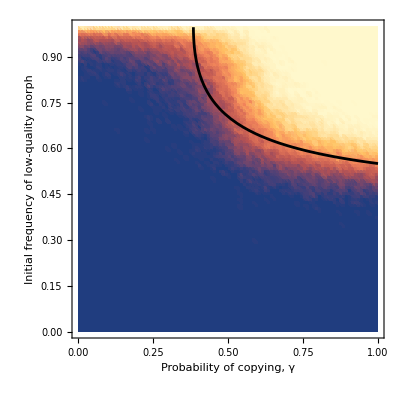

```mathematica
Show[heat2a,eq2a]
```

## Fig2b

```mathematica
rawfig2b=Import[NotebookDirectory[]<>"fig2b_data.csv","CSV"];
```

```mathematica
heat2b=ListDensityPlot[rawfig2b⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Normalised fixation time",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

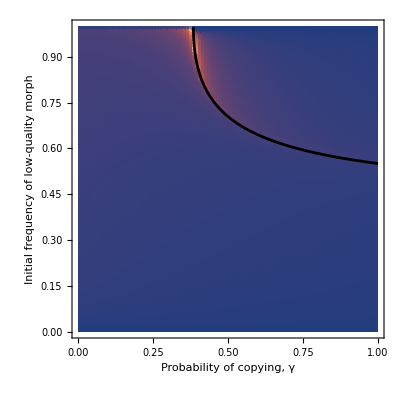

```mathematica
Show[heat2b,eq2a]
```

## Fig 2c

```mathematica
rawfig2c=Import[NotebookDirectory[]<>"fig2c_data.csv","CSV"];
```

```mathematica
heat2c=ListDensityPlot[rawfig2c⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Absolute difference in modified qualities",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

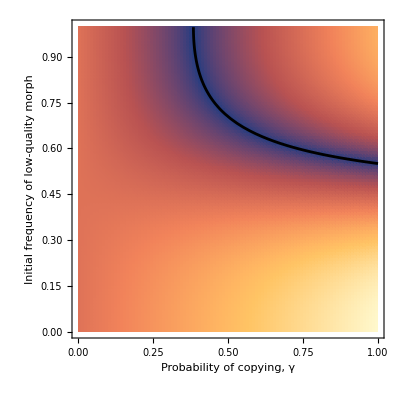

```mathematica
Show[heat2c,eq2a]
```